```mathematica
RandomReal[{1/5,2}]
```

1.90611

```mathematica
plotThemes={"Scientific","Monochrome","Detailed","Marketing","Classic"};
```

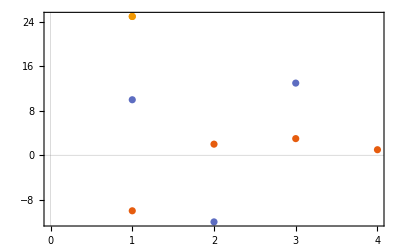
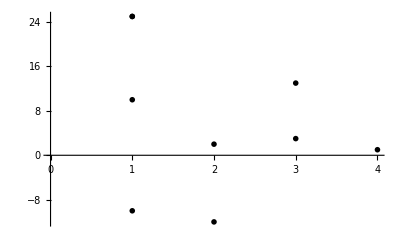
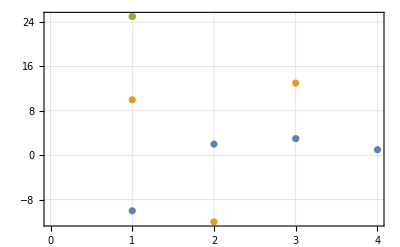
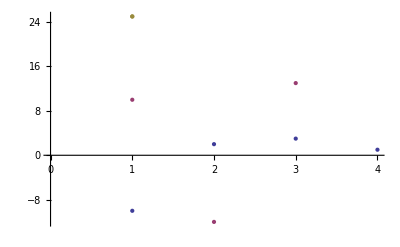
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListPlot[{{-10,2,3,1},{10,-12,13},{25}},PlotTheme->i],{i,plotThemes}]
```

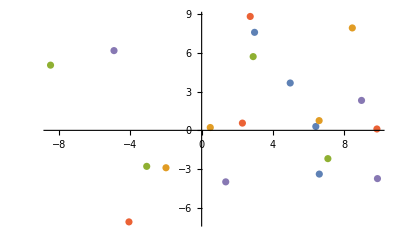

```mathematica
ListPlot@Partition[RandomReal[{-10,10},{21,2}],Round[21/5]]
```

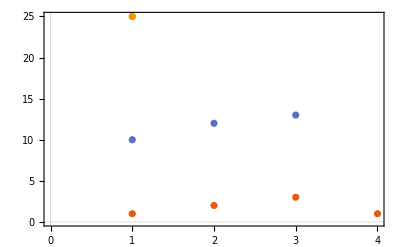

```mathematica
ListPlot[{{1,2,3,1},{10,12,13},{25}},PlotTheme->"Scientific"]
```

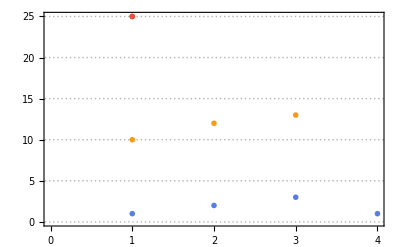

```mathematica
ListPlot[{{1,2,3,1},{10,12,13},{25}},PlotTheme->"Business"]
```

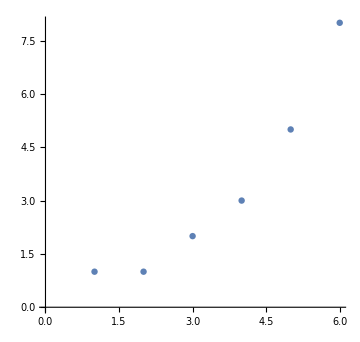

```mathematica
ListPlot[{1,1,2,3,5,8},ImageSize->{360,240},AspectRatio->RandomReal[{1/5,2}],Method->"GaussianMixture"]
```

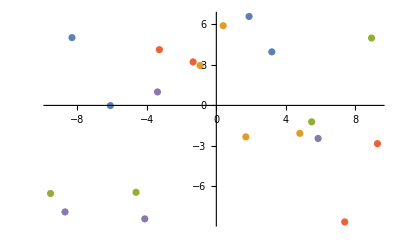

```mathematica
ListPlot[Partition[RandomReal[{-10,10},{21,2}],Round[21/5]],PlotTheme->"Default"]
```

```mathematica
RandomReal[{-80,-0.1}]
```

-32.0835

```mathematica
getRandomPointsList[range_,n_Integer,i_Integer] := Table[Partition[ RandomReal[ range, {n,2}], Round[n/5]],i ]
```

```mathematica
getRandomPointsList[{-100,100},20,5];
```

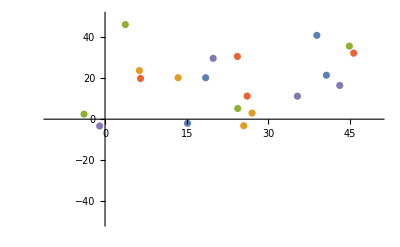

```mathematica
ListPlot[Last@getRandomPointsList[{-5,50},20,5],PlotRange->{{-10,50},{-50,50}}]
```

```mathematica
{{1},{3}}
```

```mathematica
{{5},{10},{15},{20}}
```

{{5},{10},{15},{20}}

```mathematica
range=Range[1,50,10]
```

{1,11,21,31,41}

```mathematica
range=Range[1,50,2]
```

{1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49}

```mathematica
Table[{-100 +10i, 100 +10 i},{i,5}]
```

{{-90,110},{-80,120},{-70,130},{-60,140},{-50,150}}

```mathematica
Transpose@{RandomReal[ {-90,110}, 20],RandomReal[ {0,100}, 20]}
```

{{-44.6586,29.5205},{1.26128,71.8952},{-87.5481,17.6651},{40.875,76.1037},{30.6348,73.6087},{-65.6114,43.2087},{-12.307,47.7549},{79.7953,7.06363},{33.8615,77.439},{-39.2713,65.5998},{58.5862,10.1343},{6.61226,11.2355},{-1.73715,56.4951},{-63.6012,15.9571},{66.1558,96.2059},{35.5336,62.2338},{30.3143,86.3653},{89.6903,28.4496},{4.05637,71.52},{-20.2383,55.1301}}

```mathematica
ListPlot[Partition[ RandomReal[ {-90,110}, {20,2}], Round[20/5]],PlotRange->{{-50+10,50+10},{-50,50}}]
```

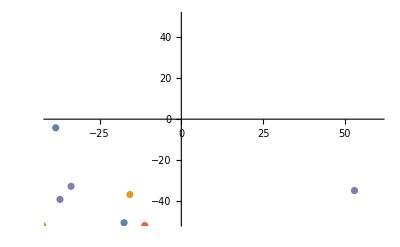

```mathematica
ListPlot[Partition[ RandomReal[ {-90,110}, {20,2}], Round[20/5]],PlotRange->{{-50+10,50+10},{-50,50}}]
```

```mathematica
getRasterizedPlots[data_] := MapIndexed[Rasterize[ListPlot[#1,PlotRange->{{-50+10First[#2],50+10First[#2]},{-50,50}}], ImageSize->{360,240}] &, data]
```

## Functions used

```mathematica
Module[{r=ranges[100,10]},
getRasterizedPlots[getRandomPointsList[20,r],r]
]
```

```mathematica
plotThemes={"Scientific","Monochrome","Detailed","Classic"}
```

```mathematica
ClearAll["Global`*"];
theme = "Monochrome";
(* Generate ranges*)
ranges[max_Integer, di_Integer]:= Flatten[Table[{{-100 + i, 0 + i},{-100 + j, 0 + j}},{i, 0, 100, 10},{j, 0, max, di}], 1]


(* generating random 2D points for the plots *)
getRandomPointsList[nPoints_Integer, ranges_] := ParallelMap[ Partition[ Transpose@{RandomReal[ First[#], nPoints],RandomReal[ Last[#], nPoints]}, Round[nPoints/5]]&, ranges]


(* generating corresponding scattered plots as images *)
getRasterizedPlots[data_,ranges_] := ParallelMap[Rasterize[ListPlot[First[#],PlotRange->Last[#],PlotTheme->theme], ImageSize->{360,240} ] &, Transpose[{data,ranges}]]


(* extracting raw axes from scattered plots *)
getRawAxes[data_,ranges_] := ParallelMap[AlphaChannel[Rasterize[ListPlot[First[#],PlotRange->Last[#],PlotStyle->Transparent,LabelStyle->Transparent,BaseStyle->{Antialiasing->False},PlotTheme->theme],Background->None,ImageSize->{360,240}]]&, Transpose[{data,ranges}] ]

(* extracting raw laberls from scattered plots*)
getRawLabels[data_,axes_,ranges_] := MapThread[ImageDifference[Binarize[AlphaChannel[Rasterize[ListPlot[#1, PlotRange-> #3, PlotStyle->Transparent, BaseStyle->{Antialiasing->False},PlotTheme->theme], Background->None, ImageSize->{360,240}]],0],#2]&,
{data, axes, ranges}
]

(* generating binarized points from scattered plots *)
getBinarizedPoints[data_,ranges_]:= ParallelMap[AlphaChannel[Rasterize[ListPlot[First[#], PlotRange->Last[#], AxesStyle->Transparent, BaseStyle->{Antialiasing->False},PlotTheme->theme], Background->None, ImageSize->{360,240}]]&, Transpose[{data,ranges}]]


(* filtering out points that are overlapping with the axes and axes labels *)
getAxes[axes_, binarizedPoints_]:= MapThread[ImageSubtract[#1, #2]&,{axes, binarizedPoints}]

getLabels[binarizedPoints_, labels_]:= MapThread[ImageSubtract[#1, #2]&,{labels, binarizedPoints}]

(* generating backgrounds from scattered plots *)
getBackgrounds[axes_,labels_,binarizedPoints_]:= MapThread[ColorNegate[ImageAdd[#1,#2,#3]]&,{axes,labels,binarizedPoints}]


(* generating image segmentations from scattered plots *)
segmentateImage[background_,axes_,labels_,binarizedPoints_]:= Round[ImageData[ImageAdd@@MapThread[ImageMultiply,{Image[{background, axes, labels, binarizedPoints},"Real32"],{1,2,3,4}}]]]

getSegmentations[dataPoints_,ranges_]:=Module[{r=ranges,data=dataPoints, binarizedPoints, axes, labels, backgrounds},
binarizedPoints=getBinarizedPoints[data,r];
axes=getAxes[getRawAxes[data,r], binarizedPoints];
labels=getLabels[binarizedPoints, getRawLabels[data, axes,r]];
backgrounds=getBackgrounds[axes, labels, binarizedPoints];
MapThread[segmentateImage[#1, #2, #3, #4]&,{backgrounds, axes, labels, binarizedPoints}]
]

(* generating training data where scattered plots are used as inputs and image segmentations are used as outputs *)
createTrainingData[max_,di_,nPoints_Integer] := Module[{ranges=ranges[max,di], data, plotsImages, segmentations},
data=getRandomPointsList[nPoints,ranges];
plotsImages= getRasterizedPlots[data,ranges];
segmentations = getSegmentations[data,ranges];
MapThread[Rule[#1, #2]&,{plotsImages, segmentations}]
]
```

```mathematica
plots=createTrainingData[20,10,50]
```

{-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1}}
 |  |  |  |

```mathematica
plots[[1,2]]//Colorize
```

-Graphics-

```mathematica
ClusteringTree[
```

```mathematica
MinMax[plots[[1,2]]]
```

{1,4}

```mathematica
plots[[1,2]]//Colorize
```

```mathematica
-Graphics-//Binarize
```

-Graphics-

```mathematica
getRasterizedPlot[nPoints_Integer,xRange_,yRange_] := Rasterize[ListPlot[Partition[ Transpose@{RandomReal[ xRange, nPoints],RandomReal[ yRange, nPoints]}, Round[nPoints/5]],PlotRange->{xRange,yRange}], ImageSize->{360,240}]
```

```mathematica
getRasterizedPlot[100,{-50,50},{-10,50}]
```

-Graphics-

Generates ranges:

```mathematica
Clear[ranges]
```

```mathematica
ranges[max_Integer,di_Integer]:=Flatten[Table[{{-100+i,0+i},{-100 +j,0+j}},{i,0,100,10},{j,0,max,di}],1]
```

```mathematica
ranges=Flatten[Table[{{-100+i,0+i},{-100 +j,0+j}},{i,0,100,10},{j,0,100,10}],1];
```

```mathematica
ParallelMap[getRasterizedPlot[100,First@#,Last@#]&,ranges]//AbsoluteTiming
```

### other old functions

```mathematica
Table[getRasterizedPlot[100,{-100+i,0+i},{-100 +j,0+j}],{i,0,100,10},{j,0,100,10}]//AbsoluteTiming
```

```mathematica
getRasterizedPlots[nPoints_Integer,nPlots_Integer] := MapIndexed[Rasterize[ListPlot[Partition[ Transpose@{RandomReal[ {-90,110}, #],RandomReal[ {0,100}, 20]}RandomReal[ #1, {nPoints,2}], Round[nPoints/5]],PlotRange->{{-50+10First[#2],50+10First[#2]},{-50,50}}], ImageSize->{360,240}] &, Table[{-100 +10i, 100 +10 i},{i,0,nPlots}]]
```

```mathematica
getRasterizedPlots[20,5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

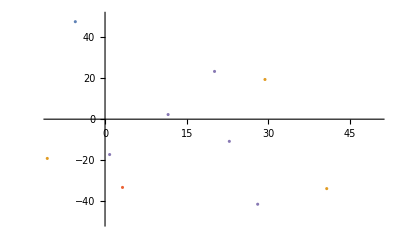

```mathematica
ListPlot[First@getRandomPointsList[{-500,500},1500,5],PlotRange->{{-10,50},{-50,50}}]
```

```mathematica
,
```

```mathematica
Part[createTrainingData[50,50,1],1,2]//Colorize
```

-Graphics-

```mathematica
RotationTransform[Part[createTrainingData[50,50,1],1,2],90]//Colorize
```

```mathematica
Rotate
```